```mathematica
sx = 0.1
q[x_] = 1/Sqrt[2Pi sx^2]Exp[-x^2/2/sx^2]
```

0.1

3.98942 ⅇ^(-50. x^2)

```mathematica
3.989422804014327 ⅇ^(-49.99999999999999 x^2)
```

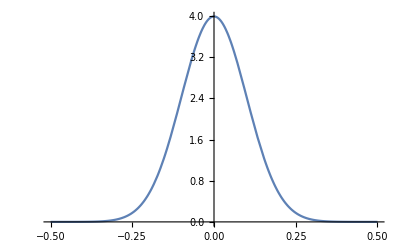

```mathematica
Plot[q[x], {x, -1, 1}, PlotRange->All]
```

```mathematica
f[x_] = Piecewise[{{x^3/Integrate[x^3, {x, 0, 3}], 0<=x<=3}}, 0]
```

Piecewise[{{(4 x^3)/81, 0≤x≤3}, {0, True}}]

```mathematica
c[x_] = Convolve[q[y], f[y], y, x]
```

-1/(Abs[-3.+x]^3 Abs[x]^3)0.0000278612 ⅇ^(-50. (-3.+x)^2-50. x^2) (-1.41421 ⅇ^(50. (-3.+x)^2) Abs[-3.+x]^3 Abs[x]^3+637.81 ⅇ^(50. x^2) Abs[-3.+x]^3 Abs[x]^3+212.132 ⅇ^(50. x^2) x Abs[-3.+x]^3 Abs[x]^3-70.7107 ⅇ^(50. (-3.+x)^2) x^2 Abs[-3.+x]^3 Abs[x]^3+70.7107 ⅇ^(50. x^2) x^2 Abs[-3.+x]^3 Abs[x]^3-717.844 ⅇ^(50. (-3.+x)^2+50. x^2) x Abs[x]^3 Erf[7.07107 Abs[-3.+x]]+717.844 ⅇ^(50. (-3.+x)^2+50. x^2) x^2 Abs[x]^3 Erf[7.07107 Abs[-3.+x]]-24167.4 ⅇ^(50. (-3.+x)^2+50. x^2) x^3 Abs[x]^3 Erf[7.07107 Abs[-3.+x]]+23954.7 ⅇ^(50. (-3.+x)^2+50. x^2) x^4 Abs[x]^3 Erf[7.07107 Abs[-3.+x]]-7976.04 ⅇ^(50. (-3.+x)^2+50. x^2) x^5 Abs[x]^3 Erf[7.07107 Abs[-3.+x]]+886.227 ⅇ^(50. (-3.+x)^2+50. x^2) x^6 Abs[x]^3 Erf[7.07107 Abs[-3.+x]]-26.5868 ⅇ^(50. (-3.+x)^2+50. x^2) x^4 Abs[-3.+x]^3 Erf[7.07107 Abs[x]]-886.227 ⅇ^(50. (-3.+x)^2+50. x^2) x^6 Abs[-3.+x]^3 Erf[7.07107 Abs[x]])

General::munfl: Exp[-849.898] is too small to represent as a normalized machine number; precision may be lost.

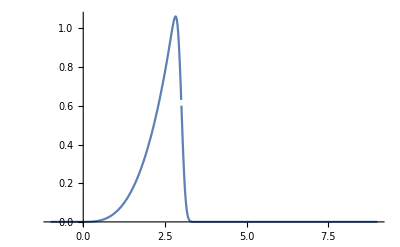

```mathematica
Plot[c[x], {x, -1, 9}, PlotRange->All]
```

```mathematica
Export["convolve_gaus_x3.json", Array[c, 1000, {-1, 9}]]
```

General::munfl: Exp[-850.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-845.005] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-840.03] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

convolve_gaus_x3.json